```mathematica
coords ={Normalize@{0,0,√(2/3)-1/(2 √(6))},Normalize@{-1/(2 √(3)),-1/2,-1/(2 √(6))},Normalize@{-1/(2 √(3)),1/2,-1/(2 √(6))},Normalize@{1/√(3),0,-1/(2 √(6))}};
Graphics3D[{Opacity[0.3], Sphere[], Opacity[1],Black, Flatten@Table[Point[c], {c, coords}],Flatten@Table[Point[c], {c, -coords}]}]
```

-Graphics3D-

```mathematica
points =PolyhedronData["Icosahedron", "VertexCoordinates"]; 

points6 = points[[6]];
points8=points[[8]];
points[[6]]=points8;
points[[8]]=points6;
points8 = points[[8]];
points7=points[[7]];
points[[7]]=points8;
points[[8]]=points7;
points10=points[[10]];
points12=points[[12]];
points[[12]]=points10;
points[[10]]=points12;
points11=points[[11]];
points12=points[[12]];
points[[11]]=points12;
points[[12]]=points11;

i=0;
points=Table[Normalize@point, {point, points}];
Labels = Table[i=i+1;Text[ToString[i], 1.3 coord], {coord, points}];
a=Graphics3D[{Arrow[{{0,0,0},{0,0,1.5}}],Arrow[{{0,0,0},{0,1.5,0}}],Arrow[{{0,0,0},{1.5,0,0}}],Opacity[0.1],PolyhedronData["Icosahedron", "Circumsphere"], Opacity[1.0],,PointSize[0.015],Point[points],Opacity[0.2],Opacity[1.0],Flatten@Labels,,Opacity[0.2],PolyhedronData["Icosahedron","Faces"],Opacity[1.0], Text[Style["S_1",Bold,24], {1.6,0,0}],Text[Style["S_2",Bold,24], {0,1.6,0}],Text[Style["S_3",Bold,24], {0,0,1.6}]}, Boxed->False]
chi1=Table[If[coord[[1]]>0,1/2 ArcCos[coord_⟦1⟧], -1/2 ArcCos[coord_⟦1⟧]],{coord,points}];
phi1 = Table[If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]],{coord, points}];
chi = Table[ArcCos[√(1/2(1+coord_⟦1⟧))], {coord, points}];
phi= Table[ArcTan[coord_⟦2⟧, coord_⟦3⟧], {coord, points}];
ϵ = Table[ArcCos[Sin[2chi[[i]]]Sin[phi[[i]]]]/2,{i,1,Length[phi]}];
α =ArcTan[Tan[2 chi] Cos[phi]]/2;


(*jones1 =Table[χ= ArcCos[coord_⟦1⟧]/2;
			ϕ1=ArcCos[coord_⟦2⟧/Sin[2χ]];
			ϕ2=ArcSin[coord_⟦3⟧/Sin[2χ]];
			ϕ3=If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]];
			{Cos[χ], Sin[χ] ⅇ^(ⅉ ϕ3)},{coord, points}];*)
jones =Table[χ= ArcCos[√(1/2(1+coord_⟦1⟧))];
			ϕ1=ArcCos[coord_⟦2⟧/Sin[2χ]];
			ϕ2=ArcSin[coord_⟦3⟧/Sin[2χ]];
			ϕ3=ArcTan[coord_⟦2⟧, coord_⟦3⟧];
			{Cos[χ], Sin[χ] ⅇ^(ⅉ ϕ3)},{coord, points}];
```

-Graphics3D-

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

```mathematica
N@chi
```

{0.785398,0.785398,1.33897,0.231824,0.380891,1.18991,0.380891,1.18991,0.925418,0.645379,0.925418,0.645379}

```mathematica
N@phi
```

{-1.5708,1.5708,-1.5708,1.5708,-2.43672,0.704872,-0.704872,2.43672,-2.65757,0.48402,-0.48402,2.65757}

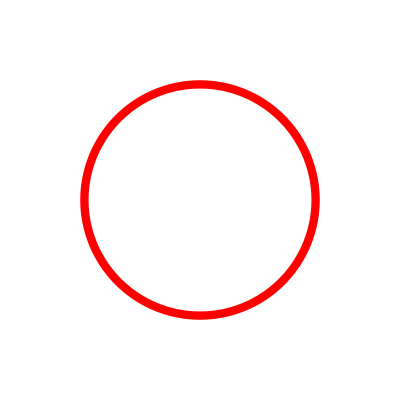
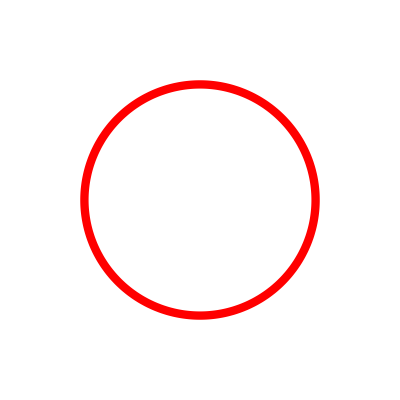
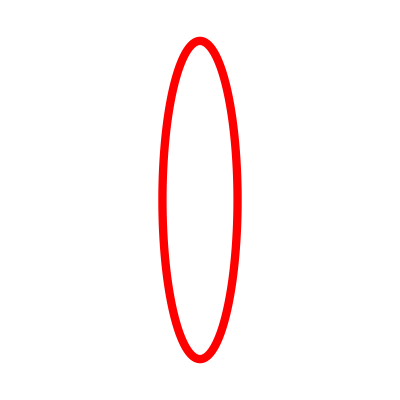
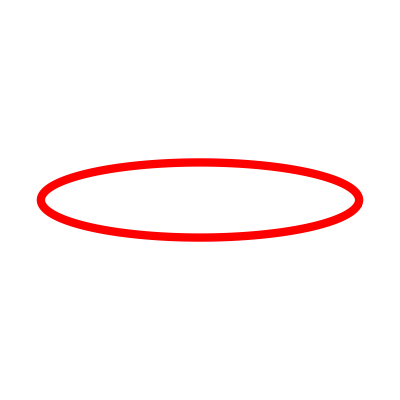
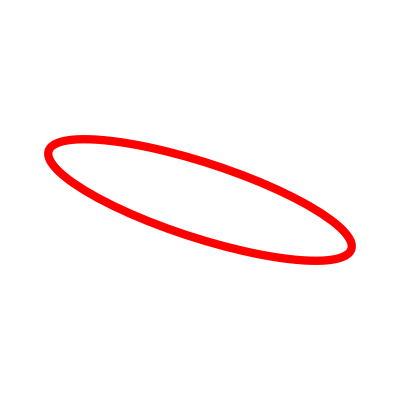
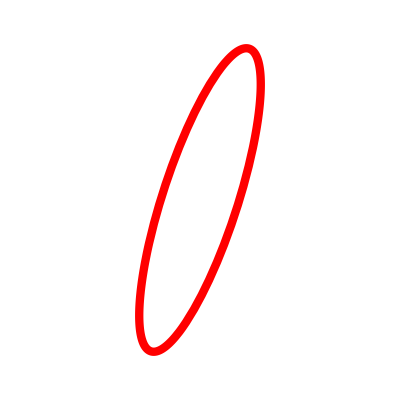
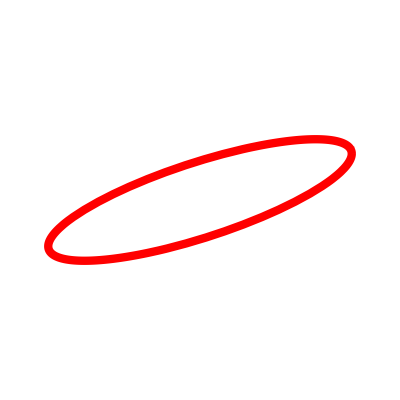
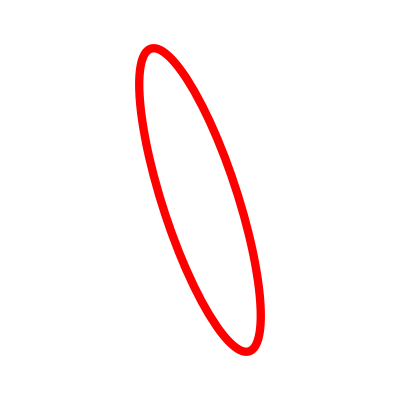

```mathematica
Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 1, Length[points]}]
```

```mathematica
data = {{-0.0092,0.0138,-0.9999},{-0.0120,-0.0112,0.9999} ,{0.8115,-0.1951,0.5508}, {-0.8588,0.1246,-0.4969},{-0.6861,-0.4870,-0.5404},{0.7206,0.4955,0.4849},{-0.7826,-0.5030,0.3667},{0.8546,0.3856,-0.3478},{0.3906,0.8553,0.3404},{-0.2152,-0.8907,-0.4006},{0.3210,0.8725,-0.3683},{-0.3912,-0.8633,0.3188}};
data1={{0.0357,0.0030,-0.9994},{-0.0234,0.0178,0.9996},{0.8752,-0.1224,0.4681},{-0.8671,0.2298,-0.4420},{-0.7469,-0.4996,-0.4387},{0.7598,0.4178,0.4981},{-0.7990,-0.4811,0.3607}, {0.7767,0.4715,-0.4176}};
stokes1 = Table[{Cos[2 chi1[[i]]], Sin[2 chi1[[i]]] Cos[phi1[[i]]], Sin[2chi1[[i]]] Sin[phi1[[i]]]}, {i, 2, 12,2}];
Graphics3D[{Opacity[0.25],Sphere[],Opacity[1],Arrow[{{0,0,0},{0,0,1.5}}],Arrow[{{0,0,0},{0,1.5,0}}],Arrow[{{0,0,0},{1.5,0,0}}],Point[stokes1], Point[-stokes1], Red,Point[data],Blue, Point[data1]}]
```

-Graphics3D-

```mathematica
N@stokes1
```

{{0.,0.,-1.},{0.894427,0.,0.447214},{-0.723607,-0.525731,-0.447214},{-0.723607,-0.525731,0.447214},{0.276393,0.850651,0.447214},{0.276393,0.850651,-0.447214}}

```mathematica
stokes = Table[{Cos[2 chi[[i]]], Sin[2 chi[[i]]] Cos[phi[[i]]], Sin[2chi[[i]]] Sin[phi[[i]]]}, {i, 1, 12}];
Graphics3D[{Opacity[0.25],Sphere[],Opacity[1],Arrow[{{0,0,0},{0,0,1.5}}],Arrow[{{0,0,0},{0,1.5,0}}],Arrow[{{0,0,0},{1.5,0,0}}],Point[stokes]}]
```

-Graphics3D-

```mathematica
Table[Dot[stokes1[[i]], data[[i]]], {i, 1, Length[stokes1],1}]
```

{0.9999,0.436436,-0.730962,0.333707,-0.845575,0.403813}

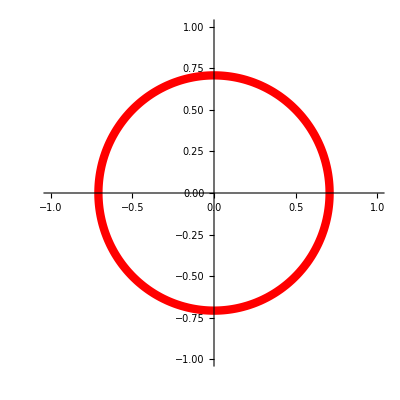
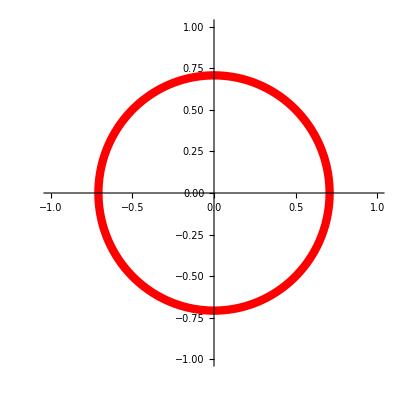
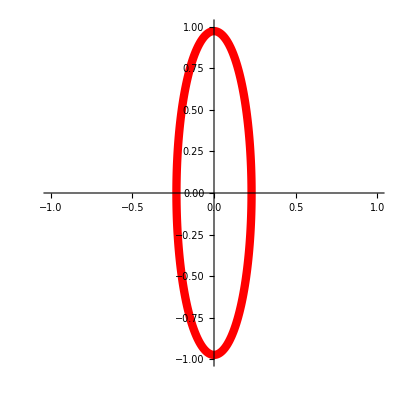
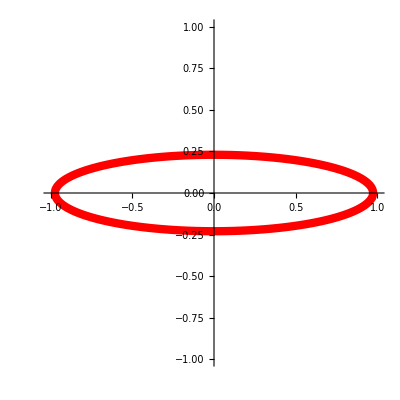
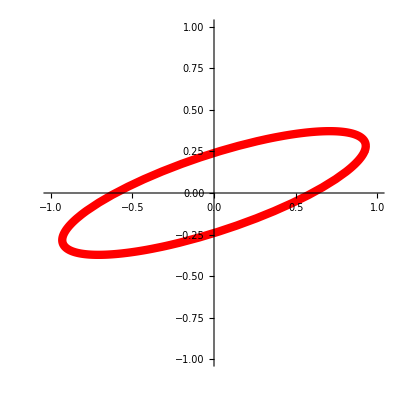
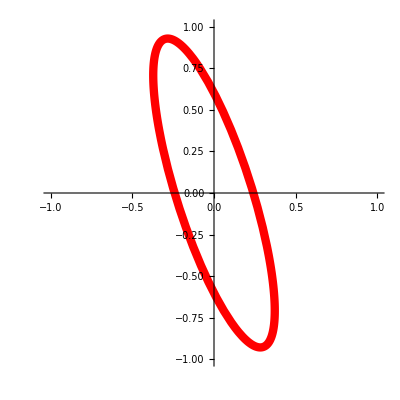
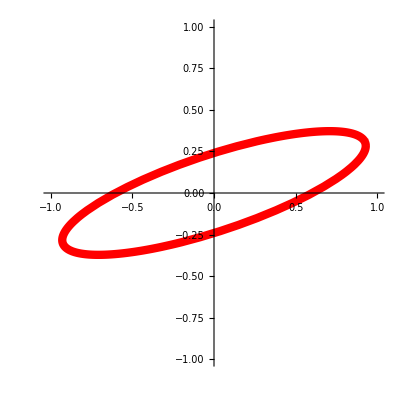
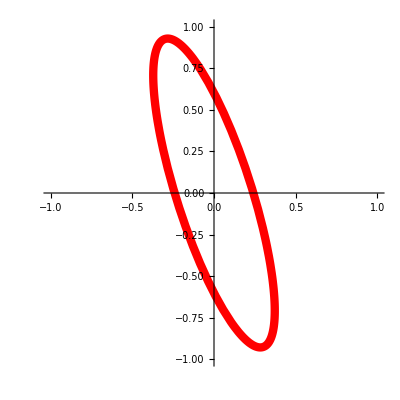

```mathematica
Table[ParametricPlot[{Cos[chi1[[j]]] Cos[t], Sin[chi1[[j]]] Cos[t-phi1[[j]]]}, {t, 0,2 π}, Axes->True, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 1, Length[points]}]
```

```mathematica
N@chi
N@phi
```

{0.785398,0.785398,1.33897,0.231824,0.380891,1.18991,0.380891,1.18991,0.925418,0.645379,0.925418,0.645379}

{-1.5708,1.5708,-1.5708,1.5708,-2.43672,0.704872,-0.704872,2.43672,-2.65757,0.48402,-0.48402,2.65757}

```mathematica
N@chi1
N@phi1
```

{-0.785398,-0.785398,-1.33897,0.231824,0.380891,-1.18991,0.380891,-1.18991,-0.925418,0.645379,-0.925418,0.645379}

{-1.5708,1.5708,-1.5708,1.5708,0.704872,0.704872,-0.704872,-0.704872,0.48402,0.48402,-0.48402,-0.48402}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["split_states.png",GraphicsRow[{GraphicsGrid[{Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 1,2}],Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 3, 4}],Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 5, 6}],Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 7,8}],Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 9, 10}],Table[ParametricPlot[{Cos[chi[[j]]] Cos[t], Sin[chi[[j]]] Cos[t-phi[[j]]]}, {t, 0,2 π}, Axes->False, PlotStyle->{Red,Arrowheads[{0.0,.1,0.1}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}]/.Line->Arrow, {j, 11, 12}]}]}],ImageResolution->500]
```

split_states.png

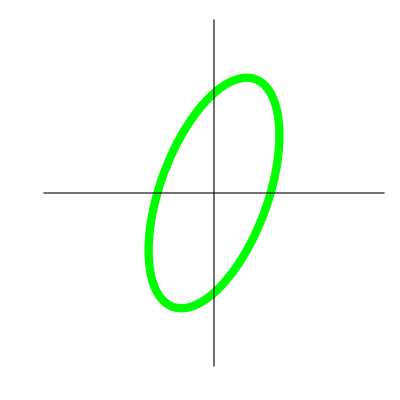

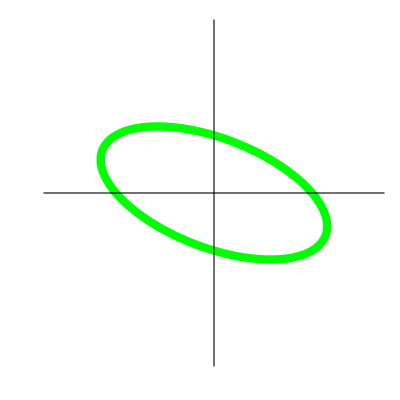

```mathematica
ϕ=-π/3;
χ=π/3;
first = ParametricPlot[{Cos[χ] Cos[t], Sin[χ] Cos[t-ϕ]}, {t, 0,2 π}, Axes->True, Ticks->False, PlotStyle->{Green,Arrowheads[{0,0,0,0.15,0,0,0,0,0.15,0,0}], Thickness[0.015]}, PlotRange->{{-1.25,1.25},{-1.25,1.25}}]/.Line->Arrow
ϕ1=-π/3;
χ1=π/3-π/2;
second =ParametricPlot[{Cos[χ1] Cos[t], Sin[χ1] Cos[t-ϕ1]}, {t, 0,2 π}, Axes->True, Ticks->False, PlotStyle->{Green,Arrowheads[{0,0,0,0.15,0,0,0,0,0.15,0,0}], Thickness[0.015]}, PlotRange->{{-1.25,1.25},{-1.25,1.25}}]/.Line->Arrow
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["first.eps", first];
Export["second.eps", second];
```

```mathematica
Export["state1.eps",Style["(κ⃗)^+e^(i SuperscriptBox[ϕ, +] (x,  y))", FontFamily->"Perpetua", FontSize->50]]
Export["state2.eps",Style["(κ⃗)^-e^(i SuperscriptBox[ϕ, -] (x,  y))", FontFamily->"Perpetua", FontSize->50]]
Export["inner_product.eps",Style["⟨(κ⃗)^+| (κ⃗)^-⟩ = 0", FontFamily->"Perpetua", FontSize->50]]
Export["matrix_eqn.eps", Style["J = R(-θ)(e^(i ϕ_x) | 0
0 | e^(i ϕ_y)) R(θ)", FontFamily->"Perpetua", FontSize->50]]
```

state1.eps

state2.eps

inner_product.eps

matrix_eqn.eps

```mathematica
Import["matrix_eqn.eps"]
```

-Graphics-

```mathematica
points =PolyhedronData["Icosahedron", "VertexCoordinates"]; 

points6 = points[[6]];
points8=points[[8]];
points[[6]]=points8;
points[[8]]=points6;
points8 = points[[8]];
points7=points[[7]];
points[[7]]=points8;
points[[8]]=points7;
points10=points[[10]];
points12=points[[12]];
points[[12]]=points10;
points[[10]]=points12;
points11=points[[11]];
points12=points[[12]];
points[[11]]=points12;
points[[12]]=points11;

i=0;
points=Table[Normalize@point, {point, points}];
Labels = Table[i=i+1;Text[ToString[i], 1.3 coord], {coord, points}];

SetDirectory["C:\Users\Noah\Dropbox\General Metasurface Polarization Splitter\Data"]
deviceVecs=Import["output_vectors.mat"];



data = {{0.4729,-0.5510,-0.7782},
{0.5271,0.4063,-0.6149},
{-0.1846, 0.7443,-0.4100},
{-0.0141,-0.0093,0.9644},
{-0.8323 ,0.2232,-0.4261}
,{-0.2334,-0.9444,-0.4300}};
data1 = {{-0.6527, 0.3968,0.6829},
{-0.7525,-0.5419,0.6825}
,{0.2973,-0.7086, 0.3161},
{-0.0115,0.0150,-0.9726},
{0.8327,-0.1131,0.4443},
{0.4131,0.9189,0.3607}};

color2=CMYKColor[0.3941,0.9683,0.6169,0.5163];
color1= CMYKColor[0.8478,0.7323,0,0];
color3= CMYKColor[0.0314,0.7351,0.6287,0.0007];
color4= CMYKColor[0.2326,0.2396,1,0.0023];
color5= CMYKColor[0.752,0.0811,1,0.0044];
color6= CMYKColor[0.1235,1,1,0.0312];

norms = Table[Normalize[vec], {vec,deviceVecs_⟦1⟧}];
norms1 = Table[Normalize[vec],{vec,deviceVecs_⟦2⟧}];
i=0;
a=Graphics3D[{Arrow[{{0,0,0},{0,0,1.5}}],Arrow[{{0,0,0},{0,1.5,0}}],Arrow[{{0,0,0},{1.5,0,0}}],Opacity[0.2],PolyhedronData["Icosahedron", "Circumsphere"], Opacity[1.0],,PointSize[0.015],Opacity[0.2],Opacity[1.0],Opacity[0.5],PolyhedronData["Icosahedron","Faces"],Opacity[1.0], Text[Style["S_1",Bold,16], {1.65,0,0}],Text[Style["S_2",Bold,16], {0,1.65,0}],Text[Style["S_3",Bold,16], {0,0,1.65}], PointSize[0.02],color1, Point[norms[[1]]],Point[norms1[[1]]],color2, Point[norms[[2]]],Point[norms1[[2]]],color3, Point[norms[[3]]],Point[norms1[[3]]],color4, Point[norms[[4]]],Point[norms1[[4]]],color5, Point[norms[[5]]],Point[norms1[[5]]],color6, Point[norms[[6]]],Point[norms1[[6]]], Black, Table[i=i+1;Text[ToString[i], 1.3 coord], {coord, norms}]}, Boxed->False,ViewPoint->{1,1,0.4}]
chi1=Table[If[coord[[1]]>0,1/2 ArcCos[coord_⟦1⟧], -1/2 ArcCos[coord_⟦1⟧]],{coord,points}];
phi1 = Table[If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]],{coord, points}];
chi = Table[ArcCos[√(1/2(1+coord_⟦1⟧))], {coord, points}];
phi= Table[ArcTan[coord_⟦2⟧, coord_⟦3⟧], {coord, points}];
ϵ = Table[ArcCos[Sin[2chi[[i]]]Sin[phi[[i]]]]/2,{i,1,Length[phi]}];
α =ArcTan[Tan[2 chi] Cos[phi]]/2;


(*jones1 =Table[χ= ArcCos[coord_⟦1⟧]/2;
			ϕ1=ArcCos[coord_⟦2⟧/Sin[2χ]];
			ϕ2=ArcSin[coord_⟦3⟧/Sin[2χ]];
			ϕ3=If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]];
			{Cos[χ], Sin[χ] ⅇ^(ⅉ ϕ3)},{coord, points}];*)



jones =Table[χ= ArcCos[√(1/2(1+coord_⟦1⟧))];
			ϕ1=ArcCos[coord_⟦2⟧/Sin[2χ]];
			ϕ2=ArcSin[coord_⟦3⟧/Sin[2χ]];
			ϕ3=ArcTan[coord_⟦2⟧, coord_⟦3⟧];
			{Cos[χ], Sin[χ] ⅇ^(ⅉ ϕ3)},{coord, points}];
SetDirectory[NotebookDirectory[]];
(*Export["dataSphere.png", a, ImageResolution->1500];*)
```

C:\Users\Noah\Dropbox\General Metasurface Polarization Splitter\Data

-Graphics3D-

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

```mathematica
"C:\\Users\\Noah\\Dropbox\\General Metasurface Polarization Splitter\\Data"
```

C:\Users\Noah\Dropbox\General Metasurface Polarization Splitter\Data

{0.0332971,0.00523346}

```mathematica
Graphics3D[{Arrow[{{0,0,0},{0,1.5,0}}],Arrow[{{0,0,0},{1.5,0,0}}],Opacity[0.4],PolyhedronData["Icosahedron", "Circumsphere"], Opacity[1.0],,PointSize[0.015],Opacity[0.2],Opacity[1.0],Opacity[0.5],PolyhedronData["Icosahedron","Faces"],Opacity[1.0], Text[Style["S_1",Bold,24], {1.65,0,0}],Text[Style["S_2",Bold,24], {0,1.65,0}],Text[Style["S_3",Bold,24], {0,0,1.65}], PointSize[0.01],Point[norms],Point[norms1]}, Boxed->False, ViewPoint->{0,0,1.5}]
```

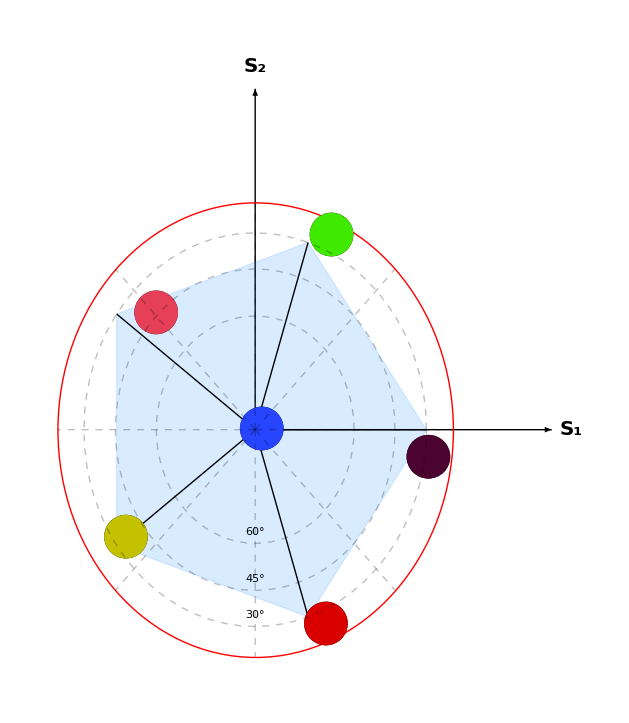

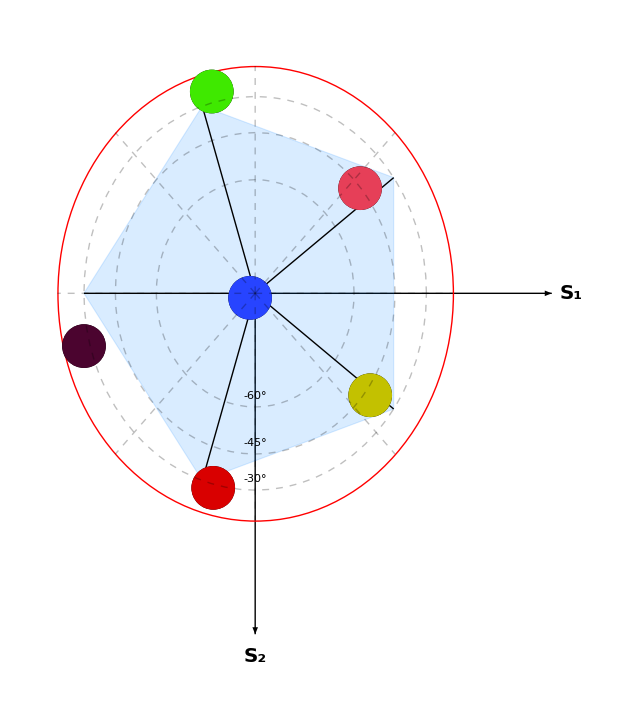

```mathematica
norms= Table[{point_⟦1⟧,point_⟦2⟧},{point,norms}];
norms1= Table[{point_⟦1⟧,point_⟦2⟧},{point,norms1}];
icosahedron = CirclePoints[{Cos[30Degree],0},5];
lines = Table[Line[{{0,0},point}],{point,icosahedron}];
fontSize = 15;
axisLabelSize = 20;

NorthernHemisphere = Graphics[{Arrow[{{0,0},{1.5,0}}],Arrow[{{0,0},{0,1.5}}],EdgeForm[Thick],Opacity[0.2],CMYKColor[{1,0.5,0,0,0.15}],Polygon[icosahedron],Black,Opacity[1.0],Thick,lines,PointSize[0.05],
,Red, Circle[],Black,Point[norms],color1,Point[norms[[1]]],color2,Point[norms[[2]]],color3,Point[norms[[3]]],color4,Point[norms[[4]]],color5,Point[norms[[5]]],color6,Point[norms[[6]]],Black,Dashed,Opacity[0.25],Table[{Rotate[Line[{{0,0},{1,0}}],θ,{0,0}](*,Rotate[Text[Style[ToString[θ 180/π]<>"°",Opacity[1],Bold,FontSize->fontSize],{1.15,0},Background->White],θ,{0,0}]*)},{θ,π/4,2π, π/4}],Table[{Circle[{0,0},√(1-h^2)],Style[Text[ToString[180/π ArcSin[h]]<>"°",{0,-√(1-h^2)+0.05}],FontSize->fontSize,Opacity[1],Bold]},{h,{1/2,(√2)/2,(√3)/2}}],Dashing[None],Opacity[1],Text[Style["S_1",Black,Bold,axisLabelSize], {1.6,0}],Text[Style["S_2",Black,Bold,axisLabelSize], {0,1.6}]}]


norms1mod =Table[{point_⟦1⟧,-point_⟦2⟧},{point,norms1}]; 


icosahedron = CirclePoints[{Cos[30Degree],π},5];
lines = Table[Line[{{0,0},point}],{point,icosahedron}];

SouthernHemisphere = Graphics[{Arrow[{{0,0},{1.5,0}}],Arrow[{{0,0},{0,-1.5}}],EdgeForm[Thick],Opacity[0.2],CMYKColor[{1,0.5,0,0,0.15}],Polygon[icosahedron],Black,Opacity[1.0],Thick,lines,PointSize[0.05],
,Red, Circle[],Black,Point[norms1mod],color1,Point[norms1mod[[1]]],color2,Point[norms1mod[[2]]],color3,Point[norms1mod[[3]]],color4,Point[norms1mod[[4]]],color5,Point[norms1mod[[5]]],color6,Point[norms1mod[[6]]],Black,Dashed,Opacity[0.25],Table[{Rotate[Line[{{0,0},{1,0}}],θ,{0,0}],(*Rotate[Text[Style[ToString[Mod[θ 180/π+180,360]]<>"°",Opacity[1],Bold,FontSize->fontSize],{1.15,0},Background->White],θ,{0,0}]*)},{θ,π/4,2π, π/4}],Table[{Circle[{0,0},√(1-h^2)],Style[Text[ToString[-180/π ArcSin[h]]<>"°",{0,-√(1-h^2)+0.05}],FontSize->fontSize,Opacity[1],Bold]},{h,{1/2,(√2)/2,(√3)/2}}],Dashing[None],Opacity[1],Text[Style["S_1",Black,Bold,axisLabelSize], {1.6,0}],Text[Style["S_2",Black,Bold,axisLabelSize], {0,-1.6}]}]
SetDirectory[NotebookDirectory[]];
Export["NorthernHemisphere.eps", NorthernHemisphere];
Export["SouthernHemisphere.eps", SouthernHemisphere];
```

```mathematica
points =PolyhedronData["Icosahedron", "VertexCoordinates"]; 

points6 = points[[6]];
points8=points[[8]];
points[[6]]=points8;
points[[8]]=points6;
points8 = points[[8]];
points7=points[[7]];
points[[7]]=points8;
points[[8]]=points7;
points10=points[[10]];
points12=points[[12]];
points[[12]]=points10;
points[[10]]=points12;
points11=points[[11]];
points12=points[[12]];
points[[11]]=points12;
points[[12]]=points11;
points=Table[Normalize@point, {point, points}];


combined = Join[norms1, norms];

s1s=Table[a_⟦1⟧, {a, combined}];
idealS1s = Table[point⟦1⟧,{point,{points[[1]],points[[3]],points[[5]],points[[7]],points[[9]],points[[11]], points[[2]],points[[4]],points[[6]],points[[8]],points[[10]],points[[12]]}}];
plot1 = ArrayReshape[Riffle[idealS1s, s1s], {2,6,2}];

s2s=Table[a_⟦2⟧, {a, combined}];
idealS2s = Table[point⟦2⟧,{point,{points[[1]],points[[3]],points[[5]],points[[7]],points[[9]],points[[11]], points[[2]],points[[4]],points[[6]],points[[8]],points[[10]],points[[12]]}}];
plot2 = N@ArrayReshape[Riffle[idealS2s, s2s], {2,6,2}];

s3s=Table[a_⟦3⟧, {a, combined}];
idealS3s = Table[point⟦3⟧,{point,{points[[1]],points[[3]],points[[5]],points[[7]],points[[9]],points[[11]], points[[2]],points[[4]],points[[6]],points[[8]],points[[10]],points[[12]]}}];
plot3 = N@ArrayReshape[Riffle[idealS3s, s3s], {2,6,2}];

fontSize = 35;
chartElementFunction="Rectangle";
pairSpacing = 0.35;
barSpacing = 0.0;
groupSpacing =0.25;
chartStyle={Blue,Red};
font="Times New Roman";

chartLabels = Table[Style[ToString[i],Black,Bold, FontFamily->"Arial CYR", FontSize->22],{i,1,6}];s1=PairedBarChart[Reverse@Abs@plot1[[1]], Reverse@Abs@plot1[[2]], PlotLabel->Style["s_1", Black,Bold, FontSize->fontSize, FontFamily->font], (*ChartLegends->{"Design", "Measured"},*) ChartLabels->{None, Reverse@chartLabels,None},ChartElementFunction->chartElementFunction,BarSpacing->{pairSpacing,groupSpacing,barSpacing},ChartStyle->chartStyle, TicksStyle->Directive[Black,Bold,FontSize->18],PlotRange->{0,1.1}]

s2=PairedBarChart[Reverse@Abs@plot2[[1]], Reverse@Abs@plot2[[2]], PlotLabel->Style["s_2", Black,Bold, FontSize->fontSize, FontFamily->font], (*ChartLegends->{"Design", "Measured"},*) ChartLabels->{None, Reverse@chartLabels,None},ChartElementFunction->chartElementFunction,BarSpacing->{pairSpacing,groupSpacing,barSpacing},ChartStyle->chartStyle,TicksStyle->Directive[Black,Bold,FontSize->18],PlotRange->{0,1.1}]

s3=PairedBarChart[Reverse@Abs@plot3[[1]], Reverse@Abs@plot3[[2]], PlotLabel->Style["s_3", Black,Bold, FontSize->fontSize, FontFamily->font], ChartLegends->{"Design", "Measured"}, ChartLabels->{None, Reverse@chartLabels,None},ChartElementFunction->chartElementFunction,BarSpacing->{pairSpacing,groupSpacing,barSpacing},ChartStyle->chartStyle,TicksStyle->Directive[Black,Bold,FontSize->18],PlotRange->{0,1.1}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["s1.eps", s1];
Export["s2.eps", s2];
Export["s3.eps", s3];
```

```mathematica
Export["berry_eqn4.eps",Style["e^(i 2  θ (x, y))|(σ⃗)^+⟩", FontFamily->"Perpetua", FontSize->50]]
```

berry_eqn4.eps

```mathematica
Export["phiY.eps",Style["|y⃗⟩", FontFamily->"Perpetua", FontSize->50]]
```

phiY.eps